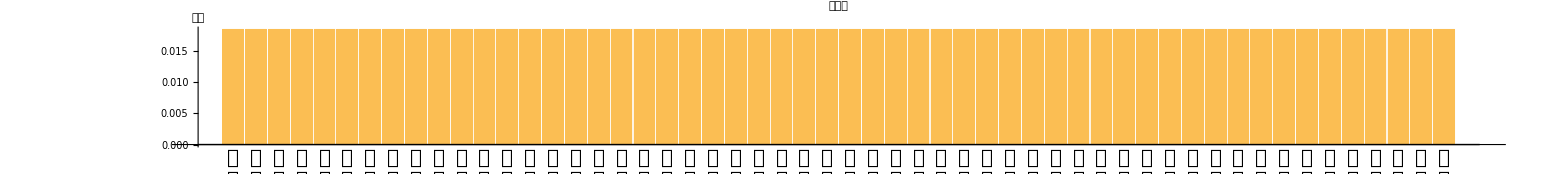

```mathematica
(*生成xlabel*)pokerLabels=Flatten[Outer[StringJoin,{"梅花","红桃","方块","黑桃"},Join[Characters["A23456789"],{"10","J","Q","K"}]]]~Join~{"大王","小王"};
pokerXLabels=pokerLabels/. s_String:>StringRiffle[Characters[s],"\n"];

(*画图*)
BarChart[ConstantArray[1/54,54],ChartLabels->Placed[pokerXLabels,Below],AxesLabel->{None,"概率"},PlotLabel->"扑克牌",ImageSize->{400*5,400},AspectRatio->1/9,LabelStyle->Directive[FontSize->20]]
```

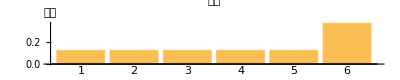

```mathematica
BarChart[{1/8,1/8,1/8,1/8,1/8,3/8},ChartLabels->{"1","2","3","4","5","6"},AxesLabel->{None,"概率"},PlotLabel->"色子",ImageSize->{400,400},AspectRatio->1/5,LabelStyle->Directive[FontSize->20]]
```

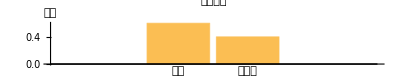

```mathematica
BarChart[{0.6,0.4},ChartLabels->{"患病","不患病"},AxesLabel->{None,"概率"},PlotLabel->"是否患病",ImageSize->{400,400},AspectRatio->1/5,LabelStyle->Directive[FontSize->20]]
```

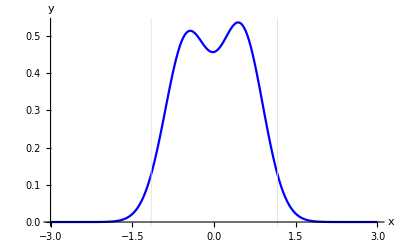

```mathematica
totalDistributionFinal2[x_]:=PDF[NormalDistribution[-0.5,0.4],x]+1.05*PDF[NormalDistribution[0.5,0.4],x];
normalizationFactorFinal2=NIntegrate[totalDistributionFinal2[y],{y,-3,3}];
normalizedDistFinal2[x_]=totalDistributionFinal2[x]/normalizationFactorFinal2;
xValues=Table[x,{x,-3,3,0.001}];
yValues=normalizedDistFinal2/@xValues;
cumulativeValues=Accumulate[yValues]*0.001;
lowerBound=xValues[[FirstPosition[cumulativeValues,_?(#>0.025&)][[1]]]];
upperBound=xValues[[FirstPosition[cumulativeValues,_?(#>0.975&)][[1]]]];
ListLinePlot[Transpose[{xValues,yValues}],PlotRange->All,AxesOrigin->{-3,0},AxesLabel->{"x","y"},GridLines->{{lowerBound,upperBound},None},GridLinesStyle->{Dashed,None},PlotStyle->Blue]
```